# SEMINARSKA NALOGA

```mathematica
RAČUNALNIŠKA ORODJA V MATEMATIKI
```

```mathematica
AJLA SOVIĆ
```

```mathematica
PROSTI PAD
```

```mathematica
Prosti pad je enakomerno pospešeno gibanje navpično navzdol, brez lastnega pogona v težnostnem polju, pri katerem na telo deluje sila teže. Pospešek pri prostem padu imenujemo težni pospešek in ga označujemo z g.
```

```mathematica
g:=9.81m/s^2
Pri prostem padu imamo enake enačbe kot pri enakomernem pospešnem gibanju, le da pospešek (a) nadomestimo z g.
hitrost[v_]:= g * t      
dolžina_poti[s_]:= g * t^2/2
Pri prostem padu ima telo v začetku hitrost 0, in mu nato narašča s težnim pospeškom g.
```

```mathematica
NALOGA I
```

```mathematica
Telo spustimo iz višine 125 m tako, da prosto pada proti tlom. Koliko časa bo padalo?
```

```mathematica
h = 125m
g = 9.81 m/s^2
```

125 m

(9.81 m)/s^2

```mathematica
čas_padanja[t_] = Sqrt[(2*h)/g]
```

5.04819 √(s^2)

```mathematica
NALOGA II
```

```mathematica
Kamen spustimo z vrha stolpnice, da prosto pade. Za pot od 8.nadstropja na višini 24m, do 7.nadstropja na višini 21m,porabi kamen čas 0.08s. S kolikšne višine smo kamen spustili?
```

```mathematica
h1 = 24m
h2 = 21m
g = 9.81m/s^2
t = 0.08 s
```

24 m

21 m

(9.81 m)/s^2

0.08 s

```mathematica
v = g * t
```

(0.7848 m)/s

```mathematica
(* h - h1 = (g*t^2)/2
h1 - h2 = v * t * (g * t^2)/2
h1 - h2 = t * Sqrt[2*g(h-h1) + [g*t^2)/2*)     (*odvisnost poti kamna od 8. do 7.nadstropja*)
h = h1 + ((h1-h2-(g*t^2)/2)^2)/(2*g*t^2)
```

94.1822 m

```mathematica
NALOGA III
```

```mathematica
Če učbenik fizike izpustimo z največjega drevesa a svetu, bo potreboval 5 sekund da pade na tla. Kolikšna je dolžina poti, ki jo je prepotoval?
```

```mathematica
t=5
g = 9.81
d = 1/2*(-g)*t^2          (*dolžina poti*)
```

5

9.81

-122.625

```mathematica
Ko vidite, da učbenik fizike ni bil poškodovan, se odločite, da boste šli na streho stavbe nebotičnika in svojo knjigo spet spustili, tokrat traja 10s. Kolikšna je zdaj dolžina poti, glede na to da je knjiga padla za dvokratno količino časa?
```

```mathematica
čas[t_]= 10
g = 9.81
dolžinaPoti[d_]=1/2(-g)*t^2
```

10

9.81

-490.5

```mathematica
idealniPodatki = Table[{i,0.5*9.81i^2},{i,5,10,1}];
Prepend[idealniPodatki,{"čas","dolžinaPoti"}]
```

{{čas,dolžinaPoti},{5,122.625},{6,176.58},{7,240.345},{8,313.92},{9,397.305},{10,490.5}}

```mathematica
(*Prepend je vgrajeni ukaz, ki na začetek seznama doda nov element. Pomočjo ukaza Table, ustvarjamo nov niz. To lahko naredimo tudi s pomočjo ukaza List*)
```

```mathematica
fitdata=Fit[idealniPodatki, {x^2,x,1},x]
```

-6.08365×10^-13+1.75193×10^-13 x+4.905 x^2

```mathematica
(*Ukaz Fit je v Mathematici namenjen aproksimaciji podatkov. Z njim bomo poskušali poiskati najboljše vrednosti*)
```

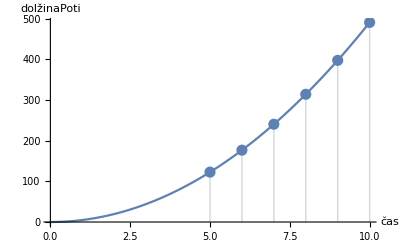

```mathematica
Show[ListPlot[idealniPodatki,AxesOrigin->{0,0},AxesLabel->{"čas","dolžinaPoti"},Filling->Axis,PlotStyle->PointSize[0.02]],Plot[fitdata,{x,0,10}]]
```

```mathematica
Zgornji graf predstavlja graf dolžine poti v odvisnosti od časa.
```

```mathematica
NEENAKOMERNO GIBANJE
```

```mathematica
Kadar se telesu pri gibanju spreminja hitrost, se telo giblje neenakomerno. Če se telesu hitrost povečuje, se telo giblje pospešno. Primer pospešnega gibanja je speljevanje avtomobila z mesta. Pospešno gibanje opišemo s pospeškom, za koliko se je telesu spremenila hitrost v določenem času.
```

```mathematica
NALOGA I
```

```mathematica
Ana se je s konstantno hitrostjo 80km/h z avtomobilom vozila proti Zagrebu. Po 20 km ji je zmanjkalo goriva, zato je šla 2km peš do najbližje črpalke. Do črpalke je potrebovala 30minut. Poiščite graf poti v odvisnosti od časa.
```

```mathematica
t = 0.5
v1 = 80
s1=20
s2=2
v2=s2/t         (*povprečna hitrost do črpalke*)
```

0.5

80

20

2

4.

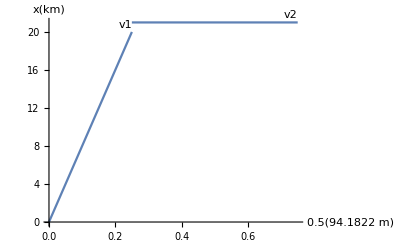

```mathematica
Slika = Show[Plot[80t,{t,0,0.25},PlotLabels->Placed["v1",Above]],Plot[20+4{0.25},{t,0.25,0.75},PlotLabels->Placed["v2",Above]],PlotRange->All,AxesLabel->{t[h],x[km]}]
```

```mathematica
TERMODINAMIKA
```

```mathematica
Temperatura je fizikalna veličina, ki se izraža s toplotnim stanjem nekega telesa in je ena od osnovnih veličin v termodinamiki. V naslednjem primeru si bomo ogledali funkcijo dolžine v odvisnosti od temperature.
```

## NALOGA I

```mathematica
Palice iz različnih materialov pri temperaturi 0 .baC merijo 1 m. Dolžina se glede na temperaturo spreminja.
L= L0(1+A*T)                  (*L0 -> dolžina pri 0 .baC, A->  temperaturni koeficient linearnega raztezka, T -> temperatura v 0 .baC*)
Temperaturni koeficienti linearnega raztezka so naslednji:Jeklo -> 6,7  10-6/.baC;Baker  -> 16,6  10-6/.baC;Aluminij -> 25.0  10-6/.baC.
```

```mathematica
L= 1
```

1

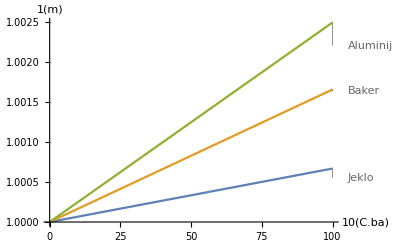

```mathematica
Plot[{1*(1+6.7*10^(-6)*t),1*(1+16.6*10^(-6)*t),1*(1+25.0*10^(-6)*t)},{t,0,100},PlotLabels->{"Jeklo","Baker","Aluminij"},AxesLabel->{t[C.ba],L[m]}]
```